```mathematica
ProID = "1LB0";
ID = "t10";
IterStep = 100;
prolen = Read[NotebookDirectory[]<>ProID<>".seq",Number];
(*numsol = Read[NotebookDirectory[]<>ProID<>".txt",Number];*)
Close[NotebookDirectory[]<>ProID<>".seq"];
```

```mathematica
(*ActualDir =  NotebookDirectory[]<>"final_runs/2ON8/full_V2/";*)
ActualDir =  NotebookDirectory[];
data=Import[ActualDir<>ID<>".sol","Table"];
ErrTable=Import[ActualDir<>ID<>".err","Table"];
(*CAerr = Import[ActualDir<>ID<>".ca","Table"];*)
```

```mathematica
NumFrames = Length[ErrTable];

newData=SplitBy[data,#=={}&];
newData=DeleteCases[newData,{{}}];


(*allAtoms =  TakeDrop[#,5*prolen] &/@newData;*)
chainData =Partition[#,prolen] &/@newData;
(*solData =#[[2]] &/@allAtoms;*)




Catom=.3;
COatom = .3;
Oatom = .3;
Natom = .3;
Cbatom = .25;
radBond=.2;
```

```mathematica
renderAllAtoms[c_]:=Graphics3D[{{Blue,Map[Sphere[#,Natom] &, c[[1]]   ]},
{Black,Map[Sphere[#,Catom] &, c[[2]]   ]},
{Black,Map[Sphere[#,COatom]&,c[[3]]   ]},{Red,Map[Sphere[#,Oatom]&,c[[4]]   ]},{Gray,Map[Sphere[#,Cbatom]&,c[[5]]    ]},Tube[  Join[ MapThread[List,{c[[2]],c[[5]]}],MapThread[List,{c[[3]],c[[4]]}],{Flatten[MapThread[List,{c[[1]],c[[2]],c[[3]]}] ,1  ] }]  ]      } ,Boxed->False]
```

```mathematica
renderAllAtoms[chainData[[NumFrames]]]
```

-Graphics3D-

```mathematica
renderChain[c_]:=Graphics3D[{{Map[Sphere[#,Catom] &, c[[2]]  ]},Tube[c[[2]]  ]      } ,Boxed->False]

table={};x=1;
While[x≤NumFrames,table=AppendTo[table,{(x-1)*IterStep,ErrTable[[x]][[1]]}];Pause[0.01];x++]

renderplot[p_] := Graphics[ListLinePlot[Take[table,p],AxesLabel->{"Iterations","Err"},PlotRange->{{0,IterStep*(NumFrames-1)},{0,0.1}},PlotRangePadding->Scaled[0.1]]]

RenderAnimation[c_,k_] := GraphicsRow[{renderChain[c],renderplot[k]},ImageSize->{800}];

anime = MapThread[RenderAnimation,{Take[chainData,NumFrames],Range[NumFrames]}];
ListAnimate[Take[anime,NumFrames],10]
```

```mathematica
Export[NotebookDirectory[]<>ProID<>".gif",ListAnimate[Take[anime,NumFrames],10]];
```

```mathematica
Table[Export[NotebookDirectory[]<>"/tmp/imgs/"<>ToString[PaddedForm[i,3,NumberPadding->{"0","0"}]]<>".png",anime[[i]]],{i,10}]
```

```mathematica
ColorData[{"TemperatureMap","Reverse"}][0.02]
```

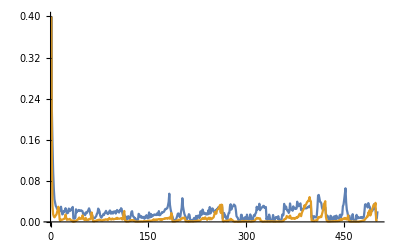

```mathematica
ListPlot[Transpose[Map[#[[{1,2}]]&,ErrTable]],Joined->True,PlotRange->{0,.4}]
```

```mathematica
movie = MapThread[renderAllAtoms,{Take[chainData,NumFrames]}];
ListAnimate[Take[movie,NumFrames],10]
```